# IPPT Model

## 5b. Backflow/Steady-State Comparison

Description:
- This notebook will import the results from “3b. Multiple-Pulse Data Export” for any propellant choice.
- Results are imported from WDX format from desired file path on PC. Auto-tethered to “Documents”.

How to Run:
- First, evaluate notebooks 1 and 2b for propellant of choice to get steady-state, multi-pulse data. Export data using 3b to create a WDX or CSV file type.
- Neutral backfill data is acquired from notebook 2c.
- Neutral backflow data is acquired from notebook 2d.
- Pull the desired file to “Documents” folder on PC, or to whichever folder Mathematica is auto-tethered.
- Either click “Evaluate Notebook” in Menu Options or import file manually.

## Data Import

Notes:
- Adjust the date the file was produced and the shot number to reflect desired data source

```mathematica
Filename1="2022-02-13_v1.12_run_21.wdx";  (* Filename1 set to backfill case *)
Filename2="2022-02-14_v1.12_run_3.wdx"; (* Filename2 set to backflow case *)
Filename3="2022-02-07_v1.12_run_9.wdx"; (* Filename3 set to multi-pulse steady-state *)

shotdata1 = Import[Filename1];
shotdata2 = Import[Filename2];
shotdata3 = Import[Filename3];
```

## Unpack Data

```mathematica
(** Dataset 1 - Backfill **)
(* ICs *)
zmax1=shotdata1[[1]];
zsteps1=shotdata1[[2]];
tmax1=shotdata1[[3]];
tsteps1=shotdata1[[4]];
zs01=shotdata1[[5]];
ws01=shotdata1[[6]];
χi01=shotdata1[[7]];
zχi1=shotdata1[[8]];
nn01=shotdata1[[9]];
zn1=shotdata1[[10]];
Te01=shotdata1[[11]];
Ti01=shotdata1[[12]];
Lc1=shotdata1[[13]];
L01=shotdata1[[14]];
Rc1=shotdata1[[15]];
C01=shotdata1[[16]];
V01=shotdata1[[17]];
zc1=shotdata1[[18]];
zc01=shotdata1[[19]];
rout1=shotdata1[[20]];
rin1=shotdata1[[21]];
frep1 = shotdata1[[22]];
Np1 =shotdata1[[23]]; 
(* Single-pulse backfill output *)
(* State variables *)
nn1=shotdata1[[24]];
ws1=shotdata1[[25]];
zs1=shotdata1[[26]];
vs1=shotdata1[[27]];
vf1=shotdata1[[28]];
ns1=shotdata1[[29]];
nf1=shotdata1[[30]];
Ic1=shotdata1[[31]];
Ip1=shotdata1[[32]];
M1=shotdata1[[33]];
V1=shotdata1[[34]];
Te1=shotdata1[[35]];
Ti1=shotdata1[[36]];
ps1=shotdata1[[37]];
KEs1=shotdata1[[38]];
Ef1=shotdata1[[39]];
(* Performance metrics *)
mbit1=shotdata1[[40]];
ms1[t_]=shotdata1[[41]];
Epi1=shotdata1[[42]];
Eel1=shotdata1[[43]];
Eind1[t_]=shotdata1[[44]];
Ecap1[t_]=shotdata1[[45]];
Eke1[t_]=shotdata1[[46]];
EkePl1[t_]=shotdata1[[47]];
EkeEnt1[t_]=shotdata1[[48]];
Ete1[t_]=shotdata1[[49]];
Ibit1[t_]=shotdata1[[50]];
Isp1[t_]=shotdata1[[51]];
ηm1[t_]=shotdata1[[52]];
MassFrac1[t_]=shotdata1[[53]];
ηT1[t_]=shotdata1[[54]];
ηTrec1[t_]=shotdata1[[55]];
Πion1[t_]=shotdata1[[56]];
Πion21[t_]=shotdata1[[57]];
Πcex21[t_]=shotdata1[[58]];

(** Dataset 2 - Multi-Pulse **)
(* ICs *)
zmax2=shotdata2[[1]];
zsteps2=shotdata2[[2]];
tmax2=shotdata2[[3]];
tsteps2=shotdata2[[4]];
zs02=shotdata2[[5]];
ws02=shotdata2[[6]];
χi02=shotdata2[[7]];
zχi2=shotdata2[[8]];
nn02=shotdata2[[9]];
zn2=shotdata2[[10]];
Te02=shotdata2[[11]];
Ti02=shotdata2[[12]];
Lc2=shotdata2[[13]];
L02=shotdata2[[14]];
Rc2=shotdata2[[15]];
C02=shotdata2[[16]];
V02=shotdata2[[17]];
zc2=shotdata2[[18]];
zc02=shotdata2[[19]];
rout2=shotdata2[[20]];
rin2=shotdata2[[21]];
frep2 = shotdata2[[22]];
Np2 =shotdata2[[23]]; 
(* Per-pulse performance metrics and nondimesionalized parameters *)
Isptable=shotdata2[[24]];
nttable=shotdata2[[25]];
ntrectable=shotdata2[[26]];
nmtable=shotdata2[[27]];
piion1table=shotdata2[[28]];
piion2table=shotdata2[[29]];
picextable=shotdata2[[30]];
(* Final state/performance *)
nn2=shotdata2[[66]];
ws2=shotdata2[[67]];
zs2=shotdata2[[68]];
vs2=shotdata2[[69]];
vf2=shotdata2[[70]];
ns2=shotdata2[[71]];
nf2=shotdata2[[72]];
Ic2=shotdata2[[73]];
Ip2=shotdata2[[74]];
M2=shotdata2[[75]];
V2=shotdata2[[76]];
Te2=shotdata2[[77]];
Ti2=shotdata2[[78]];
ps2=shotdata2[[79]];
KEs2=shotdata2[[80]];
Ef2=shotdata2[[81]];
mbit2=shotdata2[[82]];
ms2[t_]=shotdata2[[83]];
Epi2=shotdata2[[84]];
Eel2=shotdata2[[85]];
Eind2[t_]=shotdata2[[86]];
Ecap2[t_]=shotdata2[[87]];
Eke2[t_]=shotdata2[[88]];
EkePl2[t_]=shotdata2[[89]];
EkeEnt2[t_]=shotdata2[[90]];
Ete2[t_]=shotdata2[[91]];
Ibit2[t_]=shotdata2[[92]];
Isp2[t_]=shotdata2[[93]];
ηm2[t_]=shotdata2[[94]];
MassFrac2[t_]=shotdata2[[95]];
ηT2[t_]=shotdata2[[96]];
ηTrec2[t_]=shotdata2[[97]];
Πion2[t_]=shotdata2[[98]];
Πion22[t_]=shotdata2[[99]];
Πcex22[t_]=shotdata2[[100]];

(** Dataset 3 - Backflow **)
(* ICs *)
zmax3=shotdata3[[1]];
zsteps3=shotdata3[[2]];
tmax3=shotdata3[[3]];
tsteps3=shotdata3[[4]];
zs03=shotdata3[[5]];
ws03=shotdata3[[6]];
χi03=shotdata3[[7]];
zχi3=shotdata3[[8]];
nn03=shotdata3[[9]];
zn3=shotdata3[[10]];
Te03=shotdata3[[11]];
Ti03=shotdata3[[12]];
Lc3=shotdata3[[13]];
L03=shotdata3[[14]];
Rc3=shotdata3[[15]];
C03=shotdata3[[16]];
V03=shotdata3[[17]];
zc3=shotdata3[[18]];
zc03=shotdata3[[19]];
rout3=shotdata3[[20]];
rin3=shotdata3[[21]];
frep3 = shotdata3[[22]];
Np3 =shotdata3[[23]]; 
(* Per-pulse performance metrics and nondimesionalized parameters *)
Isptable=shotdata3[[24]];
nttable=shotdata3[[25]];
ntrectable=shotdata3[[26]];
nmtable=shotdata3[[27]];
piion1table=shotdata3[[28]];
piion2table=shotdata3[[29]];
picextable=shotdata3[[30]];
(* Final state/performance *)
nn3=shotdata3[[66]];
ws3=shotdata3[[67]];
zs3=shotdata3[[68]];
vs3=shotdata3[[69]];
vf3=shotdata3[[70]];
ns3=shotdata3[[71]];
nf3=shotdata3[[72]];
Ic3=shotdata3[[73]];
Ip3=shotdata3[[74]];
M3=shotdata3[[75]];
V3=shotdata3[[76]];
Te3=shotdata3[[77]];
Ti3=shotdata3[[78]];
ps3=shotdata3[[79]];
KEs3=shotdata3[[80]];
Ef3=shotdata3[[81]];
mbit3=shotdata3[[82]];
ms3[t_]=shotdata3[[83]];
Epi3=shotdata3[[84]];
Eel3=shotdata3[[85]];
Eind3[t_]=shotdata3[[86]];
Ecap3[t_]=shotdata3[[87]];
Eke3[t_]=shotdata3[[88]];
EkePl3[t_]=shotdata3[[89]];
EkeEnt3[t_]=shotdata3[[90]];
Ete3[t_]=shotdata3[[91]];
Ibit3[t_]=shotdata3[[92]];
Isp3[t_]=shotdata3[[93]];
ηm3[t_]=shotdata3[[94]];
MassFrac3[t_]=shotdata3[[95]];
ηT3[t_]=shotdata3[[96]];
ηTrec3[t_]=shotdata3[[97]];
Πion3[t_]=shotdata3[[98]];
Πion23[t_]=shotdata3[[99]];
Πcex23[t_]=shotdata3[[100]];
```

## Post-Processing Calculations

```mathematica
(* LC Frequency *)
τLC1=N[2π(C01 Lc1)^(1/2)];
τLC2=N[2π(C02 Lc2)^(1/2)];
τLC3=N[2π(C03 Lc3)^(1/2)];

(* Energy Fraction *)
EnergyFrac1[t_]=(Eke1[t]+KEs1[t])/(Eel1+Epi1-Ecap1[t]);
EnergyFrac2[t_]=(Eke2[t]+KEs2[t])/(Eel2+Epi2-Ecap2[t]); 
EnergyFrac3[t_]=(Eke3[t]+KEs3[t])/(Eel3+Epi3-Ecap3[t]); 

(* Coupling Coefficient *)
k1[t_] = M1[t]/Lc1;
k2[t_] = M2[t]/Lc2;
k3[t_] = M3[t]/Lc3;

(* Ohmic Heating *)
Eohmic1=Interpolation[Table[{tt,NIntegrate[Rc1 Ic1[dt]^2,{dt,0,tt}]},{tt,0,tmax1,tmax1/20}]];
Eohmic2=Interpolation[Table[{tt,NIntegrate[Rc2 Ic2[dt]^2,{dt,0,tt}]},{tt,0,tmax2,tmax2/20}]];
Eohmic3=Interpolation[Table[{tt,NIntegrate[Rc3 Ic3[dt]^2,{dt,0,tt}]},{tt,0,tmax3,tmax3/20}]];

(* Argon Model *)
ec=1.6 10^-19;   
me=9.11 10^-31; 
kb=1.38 10^-23;  
g0=9.81; 
γ=5/3;  
μ0=4π 10^-7; 
ϵ0=8.85 10^-12;   
σcx= 5 10^-19; 
σen=4 10^-20;  
Sion[Te_]:= 2.34 10^-14 Te^0.59 Exp[-17.44/Te]; 
Λ[ne_,Te_]:=Piecewise[{{23-Log[(ne 10^-6)^(1/2)Te^(-3/2)],Te<7.389},{24-Log[(ne 10^-6)^(1/2)Te^-1],Te≥7.389}}]
νei[ne_,Te_]:=2.91 10^-12 ne Te^(-3/2)Λ[ne,Te]
νen[nn_,Te_]:=nn σen ((8 ec Te)/(π me))^(1/2)  
ηcl[ne_,nn_,Te_]:=(me (νei[ne,Te]+νen[nn,Te]))/(ne ec^2)
δsd[Lterm_,Cp_,ne_,nn_,Te_]:=((2(ηcl[ne,nn,Te])(Lterm Cp)^(1/2))/μ0)^(1/2)  

(* Slip Losses *)
SlipLoss1[t_]=nf1[t](vs1[t]-vf1[t])UnitStep[(vs1[t]-vf1[t])];
SlipLoss2[t_]=nf2[t](vs2[t]-vf2[t])UnitStep[(vs2[t]-vf2[t])];
SlipLoss3[t_]=nf3[t](vs3[t]-vf3[t])UnitStep[(vs3[t]-vf3[t])];

(* Ionization Losses *)
IonLoss1[t_]=Sion[Te1[t]] ns1[t] nf1[t] ws1[t];
IonLoss2[t_]=Sion[Te2[t]] ns2[t] nf2[t] ws2[t];
IonLoss3[t_]=Sion[Te3[t]] ns3[t] nf3[t] ws3[t];

(* Skin Depth *)
δs1[t_]=δsd[L01+Lc1-M1[t]^2/Lc1,C01,ns1[t],nn1[zs1[t],t]+nf1[t],Te1[t]];
δs2[t_]=δsd[L02+Lc2-M2[t]^2/Lc2,C02,ns2[t],nn2[zs2[t],t]+nf2[t],Te2[t]];
δs3[t_]=δsd[L03+Lc3-M3[t]^2/Lc3,C03,ns3[t],nn3[zs3[t],t]+nf3[t],Te3[t]];

(* Transparency Parameters *)
Θem1[t_]=Exp[-3ws1[t]/δs1[t]];
Θem2[t_]=Exp[-3ws2[t]/δs2[t]];
Θem3[t_]=Exp[-3ws3[t]/δs3[t]];

Θmion1[t_]=Exp[(-ns1[t]ws1[t]Sion[Te1[t]])/vs1[t]];
Θmion2[t_]=Exp[(-ns2[t]ws2[t]Sion[Te2[t]])/vs2[t]];
Θmion3[t_]=Exp[(-ns3[t]ws3[t]Sion[Te3[t]])/vs3[t]];

Θmcex1[t_]=Exp[-ns1[t] ws1[t]σcx];
Θmcex2[t_]=Exp[-ns2[t] ws2[t]σcx];
Θmcex3[t_]=Exp[-ns3[t] ws3[t]σcx];
```

## Steady-State Comparison

```mathematica
(** Plot Styles **)
Comp2Plot[Fun1_,Fun2_,Plotlabel_,Axislabel_,scale_]:=
Plot[{Fun1[Τ τLC2]scale,Fun2[Τ τLC3]scale},{Τ,0,1},
PlotRange->{{0,1},All},
Frame->True,
AspectRatio->1,
PlotLabel-> StringJoin["Time-Evolution of ",Plotlabel],
FrameLabel->{"t / τ_LC",Axislabel},
PlotLegends->{"Backflow","Steady-State"},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
AdjComp2Plot[Fun1_,Fun2_,Plotlabel_,Axislabel_,scale_]:=
Plot[{Fun1[Τ τLC2]scale,Fun2[Τ τLC3]scale},{Τ,0.02,1},
PlotRange->{{0,1},All},
Frame->True,
AspectRatio->1,
PlotLabel-> StringJoin["Time-Evolution of ",Plotlabel],
FrameLabel->{"t / τ_LC",Axislabel},
PlotLegends->{"Backflow","Steady-State"},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
PulseCompPlot[Table1_,Table2_,Plotlabel_,Axislabel_]:=
ListLinePlot[{Table1,Table2},
PlotRange->All,
Frame->True,
ImageSize->400,
PlotLabel->StringJoin[Plotlabel," per Pulse"],
FrameLabel->{"Pulse Number",Axislabel},
PlotLegends->{"Backflow","Steady-State"},
Axes->False,
LabelStyle->{16,Black},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle-> {FontFamily->"Times"}];
GridPlot[Fun1_,Fun2_,Fun3_,Axislabel_,scale_]:=
Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC2]scale,Fun3[Τ τLC3]scale},{Τ,0,1},
PlotRange->{{0,1},All},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
AdjGridPlot[Fun1_,Fun2_,Fun3_,Axislabel_,scale_]:=
Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC2]scale,Fun3[Τ τLC3]scale},{Τ,0.02,1},
PlotRange->{{0,1},All},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];

(** Sheet Parameters **)
Print[GraphicsGrid[{
{GridPlot[zs2,zs3,"Sheet Position, z_s (m)",1],GridPlot[ws2,ws3,"Sheet Width, w_s (m)",1]},
{GridPlot[vs2,vs3,"Sheet Velocity, v_s (km/s)",10^-3],GridPlot[ns2,ns3,"Plasma Density, n_s (m^-3)",1]}}
,Spacings-> {5,-5},ImageSize-> 800]];

(** Entrained/Slipped Neutrals **)
Print[GraphicsGrid[{
{GridPlot[vf2,vf3,"Fast Neutral Velocity, v_f (km/s)",10^-3],GridPlot[nf2,nf3,"Fast Neutral Density, n_f (m^-3)",1]},
{GridPlot[ps2,ps3,"Slip Neutral Mom., p_s (μN s)",10^6],GridPlot[KEs2,KEs3,"Slip Neutral KE, KE_s (J)",1]}}
,Spacings-> {5,-5},ImageSize-> 800]];

(** Plasma **)
Print[GraphicsGrid[{
{GridPlot[Te2,Te3,"Electron Temp, T_e (eV)",1],GridPlot[Ti2,Ti3,"Ion Temp, T_i (eV)",1]},
{GridPlot[Ip2,Ip3,"Plasma Current, I_p (kA)",10^-3],GridPlot[k2,k3,"Coupling Coefficient, k",1]}}
,Spacings-> {5,-5},ImageSize-> 800]];

(** Performance **)
Print[GraphicsGrid[{
{GridPlot[Isp2,Isp3,"Specific Impulse, I_sp (s)",1],GridPlot[ηTrec2,ηTrec3,"Thrust Efficiency, η_T (%)",10^2]},
{AdjGridPlot[ηm2,ηm3,"Mass Util. Efficiency, η_m (%)",10^2],GridPlot[EnergyFrac2,EnergyFrac3,"Electrical Efficiency, η_e (%)",10^2]}}
,Spacings-> {5,-5},ImageSize-> 800]];

(** Nondimensionalized Parameters **)
Print[GraphicsGrid[{
{GridPlot[Πion2 ,Πion3,"Ionization Timescale, Π_ion",1],
AdjGridPlot[Πion22,Πion23,"Heating Fraction, Π_hf",1],
GridPlot[Πcex22,Πcex23,"CX Timescale, Π_cx",1]}},
Spacings->{5,-5}, ImageSize-> 800]];

(** Loss Mechanisms **)
Print[GraphicsGrid[{
{GridPlot[SlipLoss2,SlipLoss3,"Slip Losses, (m^-2s^-1)",1],
GridPlot[IonLoss2,IonLoss3,"Ionization Losses, (m^-2s^-1)",1]}},
Spacings->{5,-5}, ImageSize-> 800]];

(** Sheet Transparency **)
Print[GraphicsGrid[{
{GridPlot[Θem2,Θem3,"EM Transparency, Θ_e",1],
GridPlot[Θmion2,Θmion3,"Ionization Transparency, Θ_(m, ion)",1],
GridPlot[Θmcex2,Θmcex3,"CX Transparency, Θ_(m, cx)",1]}},
Spacings->{5,-5}, ImageSize-> 800]];

(** Skin Depth **)
Print[Comp2Plot[δs2,δs3,"Skin Depth","δ_s (m)",1]];
```

## Full Comparison

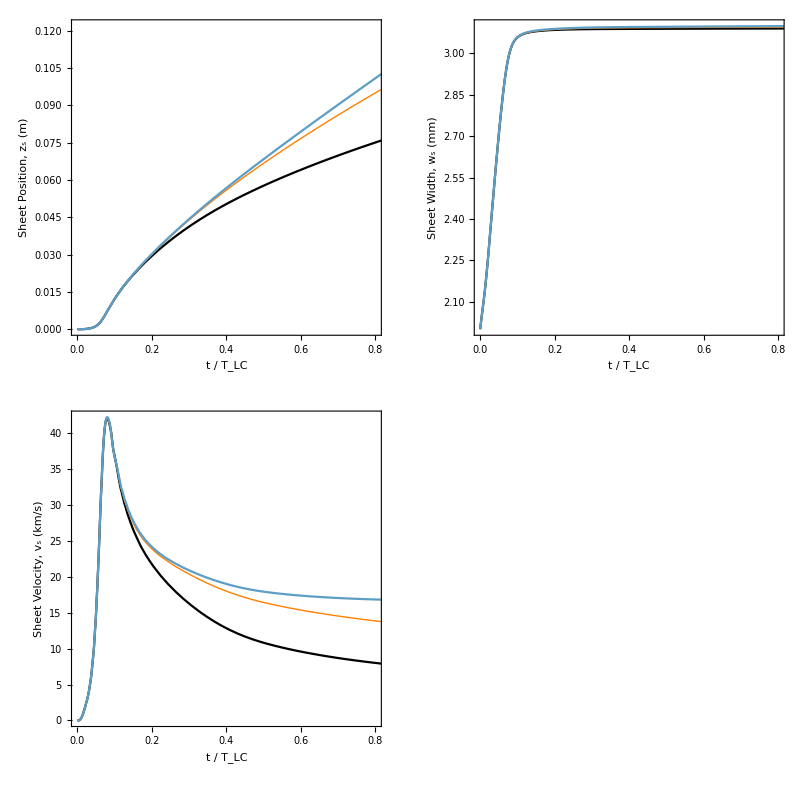

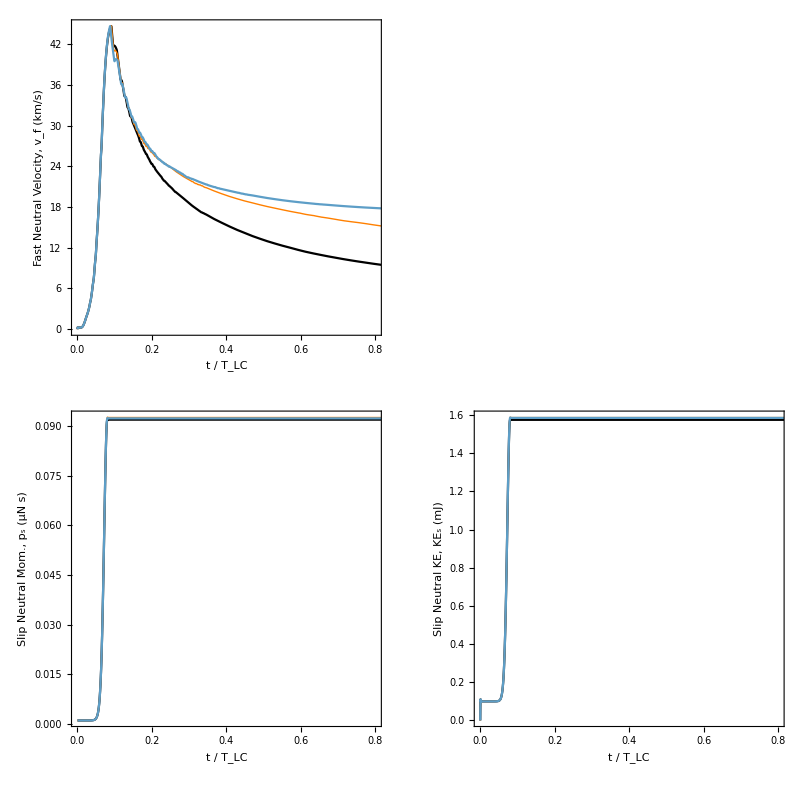

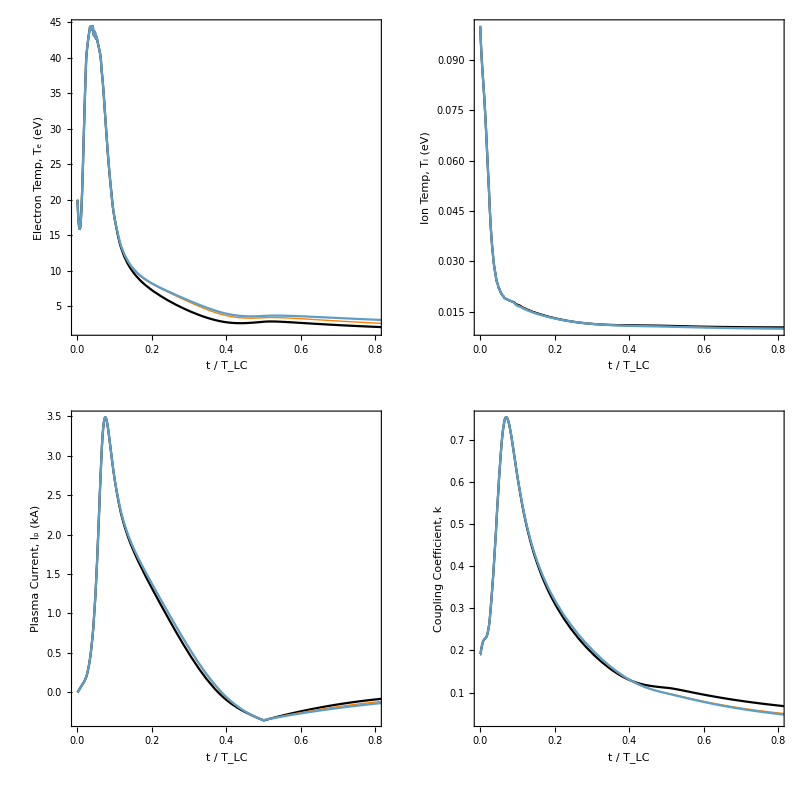

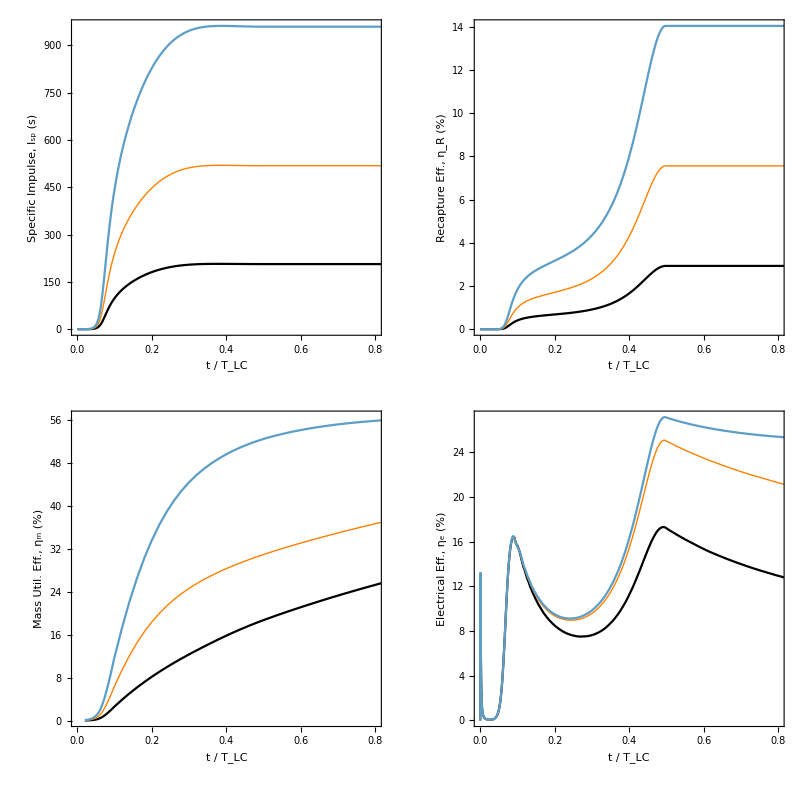

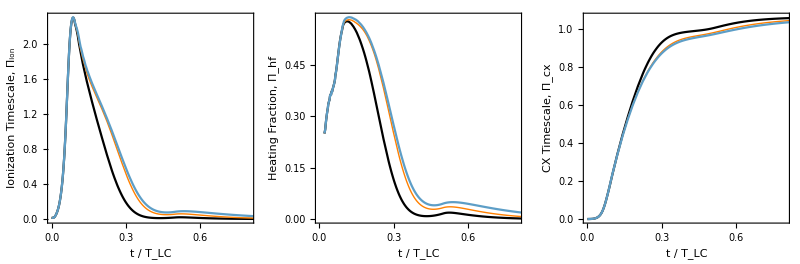

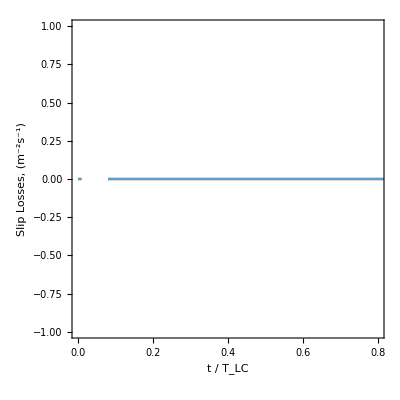

General::munfl: Exp[-1.14476×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.14526×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.14468×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

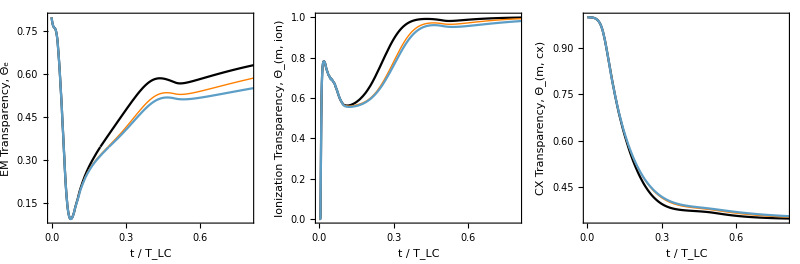

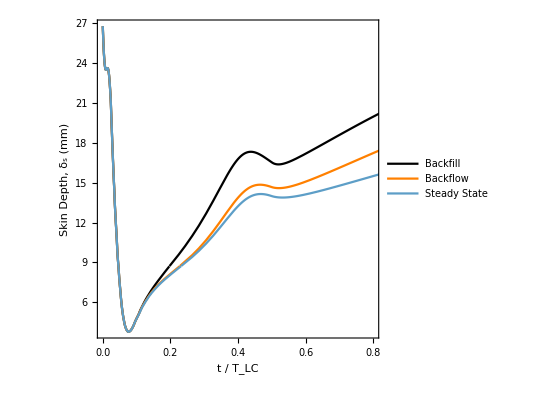

```mathematica
(** Plot Styles **)
Comp3Plot[Fun1_,Fun2_,Fun3_,Axislabel_,scale_]:=
Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC2]scale,Fun3[Τ τLC3]scale},{Τ,0,1},
PlotRange->{{0,0.8},All},
PlotStyle->{Black,{Thick,Orange},ColorData[97,"ColorList"][[7]]},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
PlotLegends->{"Backfill","Backflow","Steady State"},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
GridPlot[Fun1_,Fun2_,Fun3_,Axislabel_,scale_]:=
Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC2]scale,Fun3[Τ τLC3]scale},{Τ,0,1},
PlotRange->{{0,0.8},All},
PlotStyle->{Black,{Thick,Orange},ColorData[97,"ColorList"][[7]]},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
AdjGridPlot[Fun1_,Fun2_,Fun3_,Axislabel_,scale_]:=
Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC2]scale,Fun3[Τ τLC3]scale},{Τ,0.02,1},
PlotRange->{{0,0.8},All},
PlotStyle->{Black,{Thick,Orange},ColorData[97,"ColorList"][[7]]},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];

(** Sheet Parameters **)
Print[GraphicsGrid[{
{GridPlot[zs1,zs2,zs3,"Sheet Position, z_s (m)",1],GridPlot[ws1,ws2,ws3,"Sheet Width, w_s (mm)",10^3]},
{GridPlot[vs1,vs2,vs3,"Sheet Velocity, v_s (km/s)",10^-3],GridPlot[ns1,ns2,ns3,"Plasma Density, n_s (m^-3)",1]}}
,Spacings-> {5,-5},ImageSize-> 800]];

(** Entrained/Slipped Neutrals **)
Print[GraphicsGrid[{
{GridPlot[vf1,vf2,vf3,"Fast Neutral Velocity, v_f (km/s)",10^-3],GridPlot[nf1,nf2,nf3,"Fast Neutral Density, n_f (m^-3)",1]},
{GridPlot[ps1,ps2,ps3,"Slip Neutral Mom., p_s (μN s)",10^6],GridPlot[KEs1,KEs2,KEs3,"Slip Neutral KE, KE_s (mJ)",10^3]}}
,Spacings-> {5,-5},ImageSize-> 800]];

(** Plasma **)
Print[GraphicsGrid[{
{GridPlot[Te1,Te2,Te3,"Electron Temp, T_e (eV)",1],GridPlot[Ti1,Ti2,Ti3,"Ion Temp, T_i (eV)",1]},
{GridPlot[Ip1,Ip2,Ip3,"Plasma Current, I_p (kA)",10^-3],GridPlot[k1,k2,k3,"Coupling Coefficient, k",1]}}
,Spacings-> {5,-5},ImageSize-> 800]];

(** Performance **)
Print[GraphicsGrid[{
{GridPlot[Isp1,Isp2,Isp3,"Specific Impulse, I_sp (s)",1],GridPlot[ηTrec1,ηTrec2,ηTrec3,"Recapture Eff., η_R (%)",10^2]},
{AdjGridPlot[ηm1,ηm2,ηm3,"Mass Util. Eff., η_m (%)",10^2],GridPlot[EnergyFrac1,EnergyFrac2,EnergyFrac3,"Electrical Eff., η_e (%)",10^2]}}
,Spacings-> {5,-5},ImageSize-> 800]];

(** Nondimensionalized Parameters **)
Print[GraphicsGrid[{
{GridPlot[Πion1 ,Πion2,Πion3,"Ionization Timescale, Π_ion",1],
AdjGridPlot[Πion21,Πion22,Πion23,"Heating Fraction, Π_hf",1],
GridPlot[Πcex21,Πcex22,Πcex23,"CX Timescale, Π_cx",1]}},
Spacings->{5,-5}, ImageSize-> 800]];

(** Loss Mechanisms **)
Print[GraphicsGrid[{
{GridPlot[SlipLoss1,SlipLoss2,SlipLoss3,"Slip Losses, (m^-2s^-1)",1],
GridPlot[IonLoss1,IonLoss2,IonLoss3,"Ionization Losses, (m^-2s^-1)",1]}},
Spacings->{5,-5}, ImageSize-> 800]];

(** Sheet Transparency **)
Print[GraphicsGrid[{
{GridPlot[Θem1,Θem2,Θem3,"EM Transparency, Θ_e",1],
GridPlot[Θmion1,Θmion2,Θmion3,"Ionization Transparency, Θ_(m, ion)",1],
GridPlot[Θmcex1,Θmcex2,Θmcex3,"CX Transparency, Θ_(m, cx)",1]}},
Spacings->{5,-5}, ImageSize-> 800]];

(** Skin Depth **)
Print[Comp3Plot[δs1,δs2,δs3,"Skin Depth, δ_s (mm)",10^3]];
```